```mathematica
<<IGraphM`
```

IGraph/M 0.4 (April 2, 2020)
Evaluate IGDocumentation[] to get started.

```mathematica
ClearAll[f,HammingGraph]
```

```mathematica
HammingGraph[d_,q_,h_Integer:1,opts:OptionsPattern[]]:=HammingGraph[d,q,h,opts]=With[{v=Tuples[Range[0,q-1],d]},Graph[v,TwoWayRule@@@Select[Subsets[v,{2}],HammingDistance@@#==h&],opts]]
```

```mathematica
f[d_,q_]:=f[d,q]=MinimalBy[Subgraph[HammingGraph[d,q],Append[#,ConstantArray[0,d]]]&/@Subsets[Rest@Tuples[Range[0,q-1],d],{Floor[q^d/2]}],Max@VertexDegree[#]&]
```

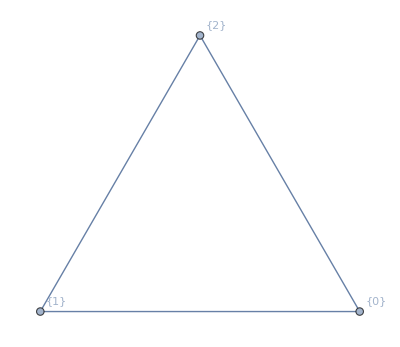

```mathematica
GraphPlot[First[#],VertexLabels->Automatic]&/@Gather[f[1,4],IsomorphicGraphQ]
```

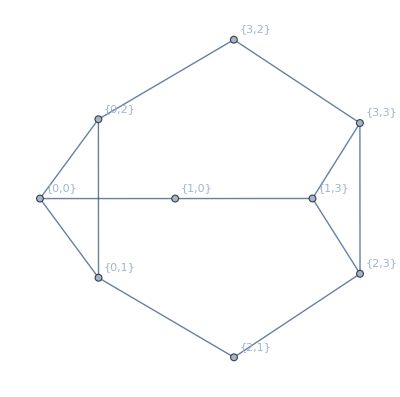

```mathematica
GraphPlot[First[#],VertexLabels->Automatic]&/@Gather[f[2,4],IsomorphicGraphQ]
```

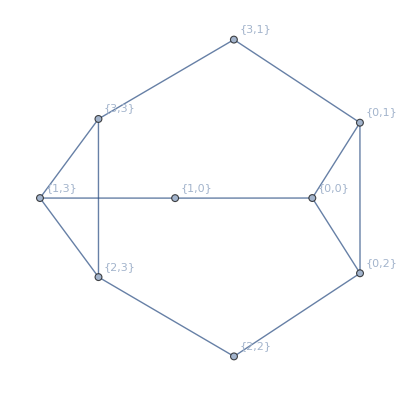
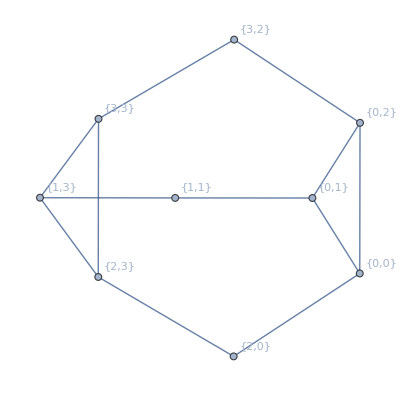
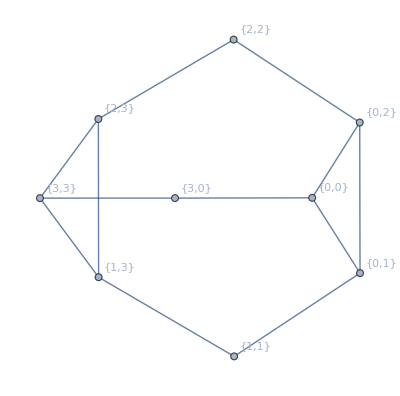
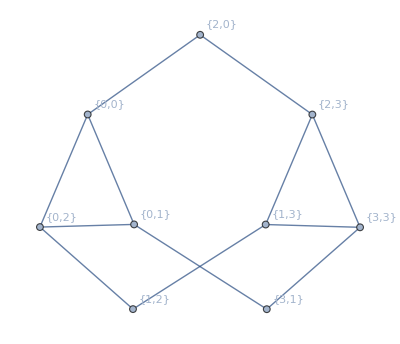
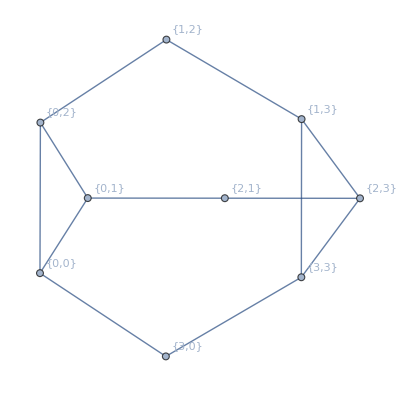
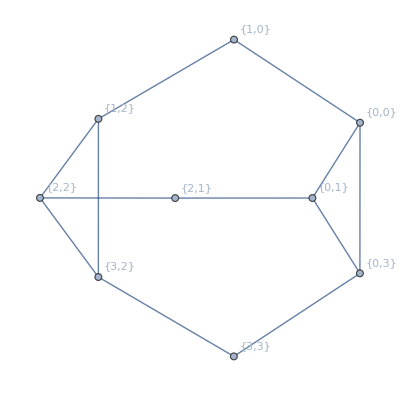
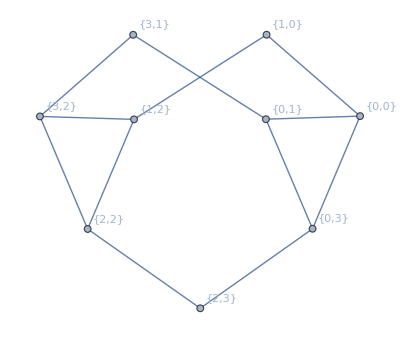
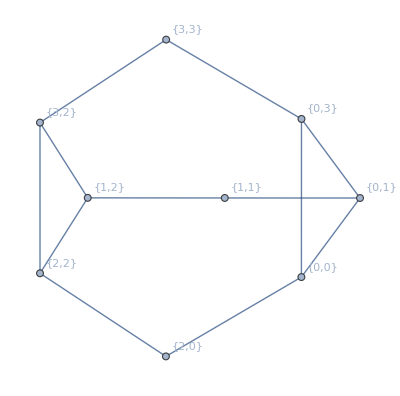
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
f[2,4]
```

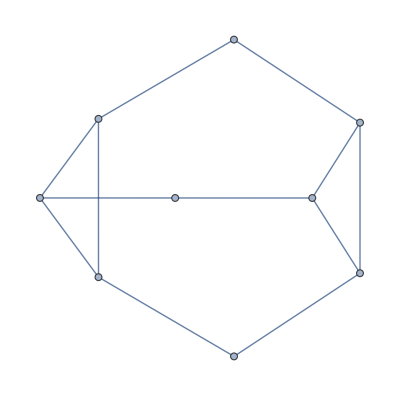

```mathematica
Subgraph[HammingGraph[2,4],{{0,0},{0,1},{0,2},{1,3},{2,3},{3,3},{1,0},{2,1},{3,2}}]
```

```mathematica
FindIndependentVertexSet[%4,{4},All]
```

{{{0,0},{1,3},{2,1},{3,2}},{{0,2},{3,3},{1,0},{2,1}},{{0,1},{2,3},{1,0},{3,2}}}

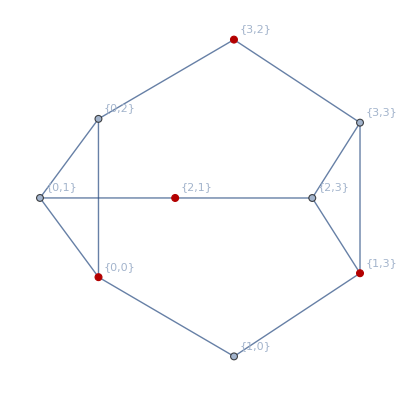
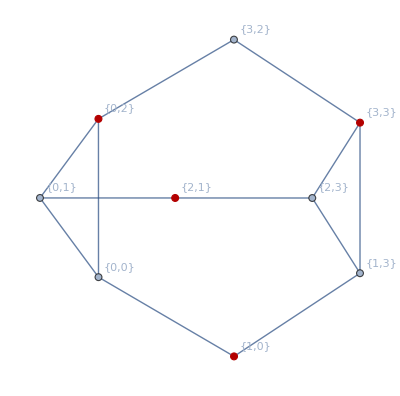
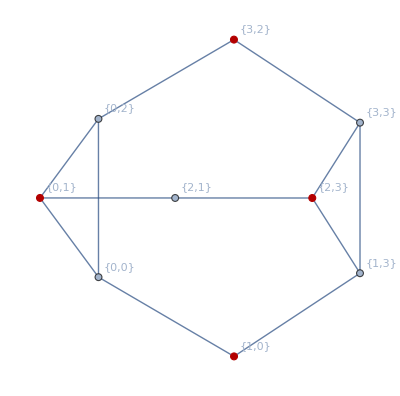

```mathematica
GraphPlot[HighlightGraph[%4,#],VertexLabels->Automatic]&/@%12
```


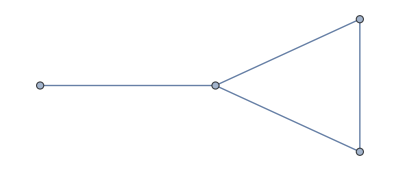

```mathematica
f[4]=Subgraph[HammingGraph[3,4],#]&/@{{{0,0,0},{0,0,1},{0,1,0},{1,0,0}},{{0,0,0},{0,0,1},{0,0,2},{0,1,0}}}
```

```mathematica
f[n_]:=f[n]=DeleteDuplicates[Select[Flatten@Table[Subgraph[HammingGraph[3,4],Append[s,#]]&/@Complement[AdjacencyList[HammingGraph[3,4],s],s],{s,VertexList/@f[n-1]}],Max@VertexDegree[#]≤3&],IsomorphicGraphQ]
```

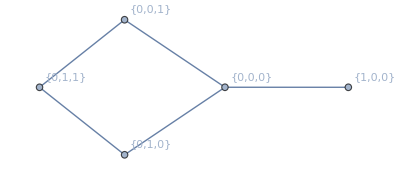
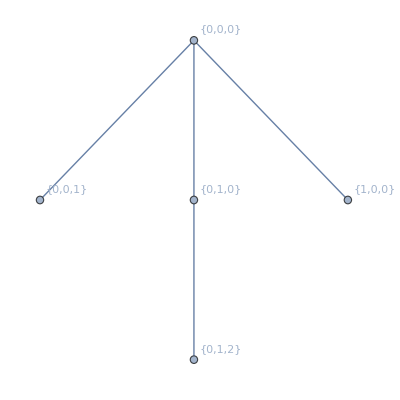
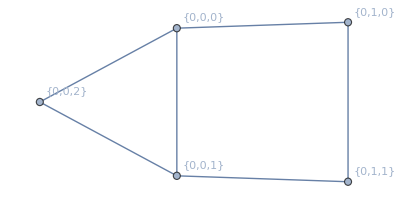
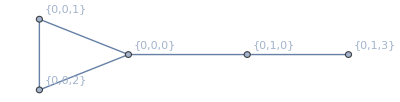
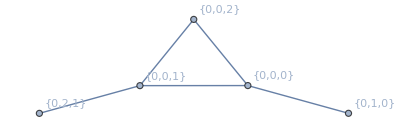

```mathematica
GraphPlot[#,VertexLabels->Automatic]&/@f[5]
```

```mathematica
Table[Length@f[n],{n,4,10}]
```

{2,5,15,29,77,184,536}

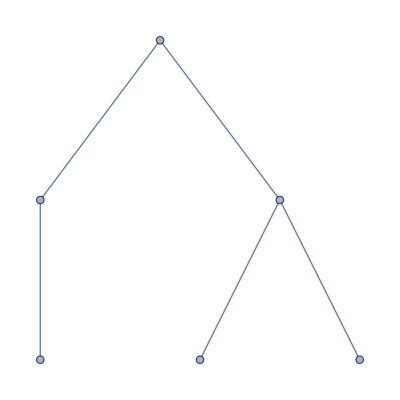
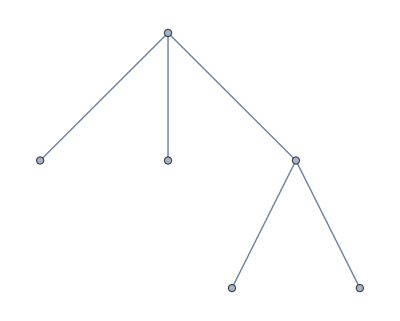
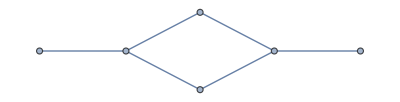
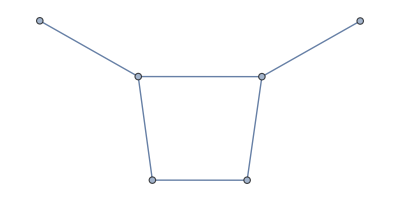
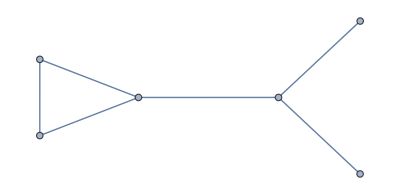
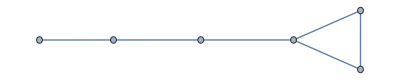
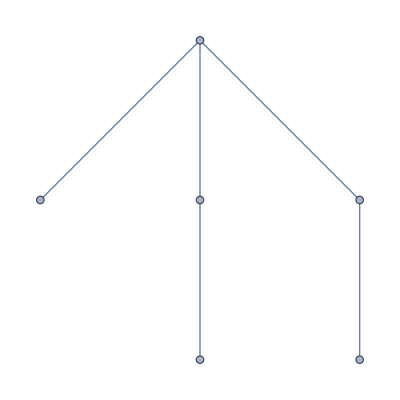
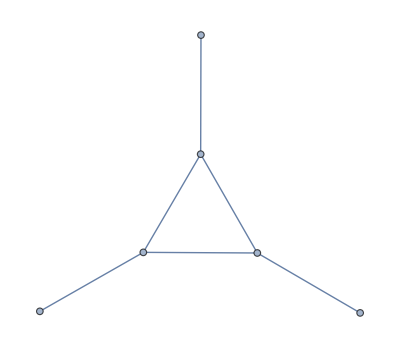

```mathematica
IGImportString["E?NO
E?dg
E?lo
E@hW
E@ow
E@po
EAIW
ECSw
ECXo
EELg
EGcw
EKSw
ETXW
E`dg
E`ow
E{Sw

","Nauty"]
```

```mathematica
%7//Length
```

16

```mathematica
f[6]//Length
```

15

```mathematica
First@Complement[%7,f[6],SameTest->IsomorphicGraphQ]
```

-Graphics-

```mathematica
IGLADSubisomorphicQ[%13,HammingGraph[3,4],"Induced"->True]
```

True

```mathematica
Normal[ToString/@First@IGLADGetSubisomorphism[%13,HammingGraph[3,4],"Induced"->True]]
```

{1→{0, 0, 0},2→{3, 0, 0},3→{1, 2, 1},4→{1, 1, 1},5→{1, 0, 0},6→{1, 0, 1}}

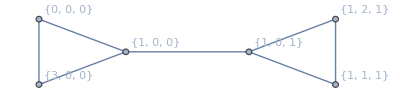

```mathematica
GraphPlot[%13,VertexLabels->%15]
```

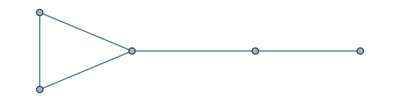
```mathematica
GraphPlot[-Graphics-,VertexLabels->Automatic]
```

-Graphics-

```mathematica
DeleteCases[Values@First@IGLADGetSubisomorphism[%13,HammingGraph[3,4],"Induced"->True],{1,1,1}]
```

{{0,0,0},{3,0,0},{1,2,1},{1,0,0},{1,0,1}}

```mathematica
VertexList[-Graphics-]
```

{{0,0,0},{0,0,1},{0,0,2},{0,1,0},{0,1,3}}

```mathematica
IsomorphicGraphQ[Subgraph[HammingGraph[3,4],%30],Subgraph[HammingGraph[3,4],%31]]
```

True

```mathematica
IsomorphicGraphQ[VertexDelete[HammingGraph[3,4],%30],VertexDelete[HammingGraph[3,4],%31]]
```

False